```mathematica
(* Función para determinar el centro de la circunferencia sobre la que se moverá el auto *)
(* La función resultante es la final *)
```

```mathematica
Solve[(Ax-Cx)^2+(Ay-Cy)^2==(Px-Cx)^2+(Py-Cy)^2,{Cx, Cy}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Cy→-(Cx (Ax-Px))/(Ay-Py)-(-Ax^2-Ay^2+Px^2+Py^2)/(2 (Ay-Py))}}

```mathematica
Cy[Cx_]:=(Ax^2+Ay^2-2 Ax Cx+2 Cx Px-Px^2-Py^2)/(2 Ay-2 Py)
```

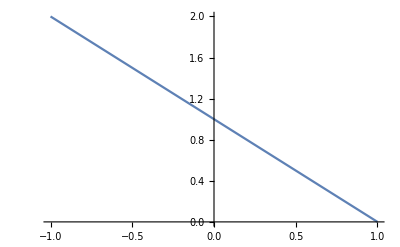

```mathematica
Plot[Cy[x]/.{Ax->1, Ay->1, Px->0, Py->0},{x,-1,1}]
```

```mathematica
Solve[D[x^2+y[x]^2==r^2,x],y'[x]]
```

{{y'[x]→-x/y[x]}}

```mathematica
Solve[ArcTan[-x/y[x]]==θ,{x,y[x]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y[x]→ConditionalExpression[-x Cot[θ], ]}}

```mathematica
β[{Ax_,Ay_},{Px_,Py_}]:=-(-Ax^2-Ay^2+Px^2+Py^2)/(2 (Ay-Py));
α[{Ax_,Ay_},{Px_,Py_}]:=-(Ax-Px)/(Ay-Py);
```

```mathematica
β/(α+Cot[θ])//Simplify
```

(-Ax^2-Ay^2+Px^2+Py^2)/(2 (Ax-Px+(-Ay+Py) Cot[θ]))

```mathematica
X[θ_,{Ax_,Ay_},{Px_,Py_}]:=(-Ax^2-Ay^2+Px^2+Py^2)/(2 (Ax-Px+(-Ay+Py) Cot[θ]))
Y[θ_,A_,P_]:=α[A,P]*X[θ,A,P]+β[A,P]
```

```mathematica
θ1=100*Pi/180;
A={2,0.5};
P={-1,3};
cx=X[θ1,A,P]//N
cy=Y[θ1,A,P]//N
(* r *)
Sqrt[(A[[1]]-cx)^2+(A[[2]]-cy)^2]
```

1.12341

2.49809

2.18192

```mathematica
X[θ, {ax,ay},{px,py}]
Y[θ, {ax,ay},{px,py}]
```

(-ax^2-ay^2+px^2+py^2)/(2 (ax-px+(-ay+py) Cot[θ]))

-(-ax^2-ay^2+px^2+py^2)/(2 (ay-py))-((ax-px) (-ax^2-ay^2+px^2+py^2))/(2 (ay-py) (ax-px+(-ay+py) Cot[θ]))

```mathematica
ArcTan[(ay-Y[θ, {ax,ay},{px,py}])/(ax-X[θ, {ax,ay},{px,py}])]
```

ArcTan[(ay+(-ax^2-ay^2+px^2+py^2)/(2 (ay-py))+((ax-px) (-ax^2-ay^2+px^2+py^2))/(2 (ay-py) (ax-px+(-ay+py) Cot[θ])))/(ax-(-ax^2-ay^2+px^2+py^2)/(2 (ax-px+(-ay+py) Cot[θ])))]